# Multiway Systems and Quantum Circuits

Authors: Furkan Semih Dündar, Xerxes D. Arsiwalla, Hatem Elshatlawy
Year: 2025
License: CC BY-SA 4.0

## Software

```mathematica
(*PacletInstall["Wolfram/QuantumFramework"]*)
```

```mathematica
Needs["Wolfram`QuantumFramework`"]
```

## Quantum Circuits

```mathematica
qc1=QuantumCircuitOperator[{"XX","CNOT"}];
```

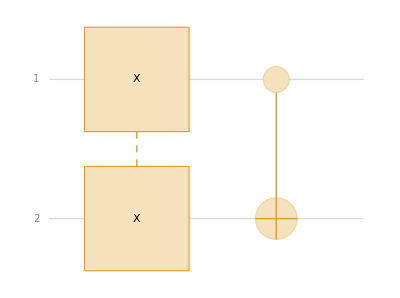

```mathematica
qc1["Diagram",ImageSize->Tiny]
```

```mathematica
qc2=QuantumCircuitOperator[{"YY","CNOT"}];
```

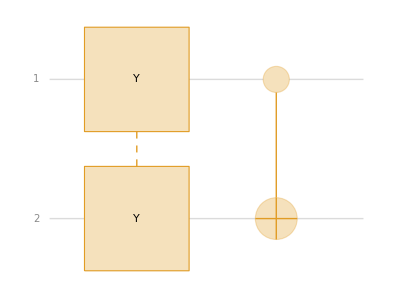

```mathematica
qc2["Diagram",ImageSize->Tiny]
```

```mathematica
qc3=QuantumCircuitOperator[{"ZZ","CNOT"}];
```

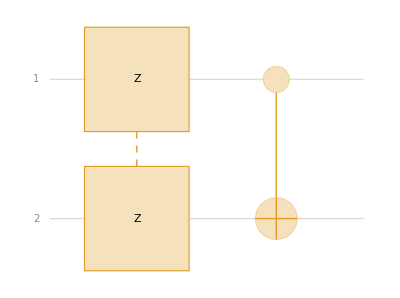

```mathematica
qc3["Diagram",ImageSize->Tiny]
```

## The Multiway System

```mathematica
g=Graph[Range[12],{1->8,4->5,2->7,3->6,5->9,6->10,7->12,8->11,1->5,4->8,2->6,3->7},VertexCoordinates->{1->{0,0},2->{1,0},3->{2,0},4->{3,0},5->{0,-1},6->{1,-1},7->{2,-1},8->{3,-1},9->{0,-2},10->{1,-2},12->{3,-2},11->{2,-2}},ImageSize->Small,PlotTheme->"VibrantColor",VertexSize->Small]
```

-Graphics-

## Plot

```mathematica
plt=GraphicsRow[{
Show[g,PlotLabel->"a)"],
qc1["Diagram",PlotLabel->"b)",ImageSize->Small],qc2["Diagram",PlotLabel->"c)",ImageSize->Small],
qc3["Diagram",PlotLabel->"d)",ImageSize->Small]
},Dividers->{{2->Directive[Dashed],3->Directive[Dashed],4->Directive[Dashed]},False},Alignment->Top]
```

-Graphics-